```mathematica
OS="win";(*or linux*)
Needs["ErrorBarPlots`"];
Needs["EDA`"];
If[OS=="win",
Print["Working Directory: ",curDir=SetDirectory["C:\\Users\\Prajwal\\Dropbox\\nEDM\\psi-nedm\\Analysis"]];
Print["(ASCII) Rawdata Directory: ",AscDir="C:\\Users\\Prajwal\\Dropbox\\nEDM\\rawdata"];
];
If[OS=="linux",
Print["Working Directory:",curDir=SetDirectory["/home/prajwal/Dropbox/nEDM/psi-nedm/Analysis"]];
Print["(faster) Rawdata Directory:",fastDir="/home/prajwal/nEDM/rawdata"];
Print["(ASCII) Rawdata Directory:",AscDir="/home/prajwal/Dropbox/nEDM/rawdata"];
];
Print["Runs in the list: ",runNum={010119,10124,10166,10189,10246,10270,10273,10281,10345,10386,10391,10417,10420,10463,10471,10497,11159,11166,11239,11277,11305,11357,11363,11409,11412}];(*{010119,10124,10135,10166,10189,10191,10207,10246,10270,10273,10281,10345,10386,10391,10417,10420,10463,10471,10497,10541},{11159,11166,11208,11239,11277,11305,11357,11363,11409,11412,11445,11448},{11159,11166,11239,11277,11305,11357,11363,11409,11412}*)
Print["#Runs in the list: ",runn=Dimensions[runNum][[1]]];
metaStructure={Real,Word,Real,Real,Real,Real,Real};
metaStructure2={Word,Real,Real,Word,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real};
histbeg=100;histlast=1400;ChNum=1;
chnum={1,2,3,4,5,6,7,8,9,11,12,13,14,15,16,17,18,19};
steps={28,2,2,2,2,20,160,2,2,64,1};(**)
Print["Number of Steps: ",Dimensions[steps][[1]]];
(*6->HV, SF1->25, SF2->26, cRF->-1, UP->27, DOWN->28, Monitor->30, Filling->31, Total->32*)
```

Working Directory: C:\Users\Prajwal\Dropbox\nEDM\psi-nedm\Analysis

(ASCII) Rawdata Directory: C:\Users\Prajwal\Dropbox\nEDM\rawdata

Runs in the list: {10119,10124,10166,10189,10246,10270,10273,10281,10345,10386,10391,10417,10420,10463,10471,10497,11159,11166,11239,11277,11305,11357,11363,11409,11412}

#Runs in the list: 25

Number of Steps: 11

## Needs at least 224 (4*56) cycles to determine full SF efficiencies

## For Runs (.info)

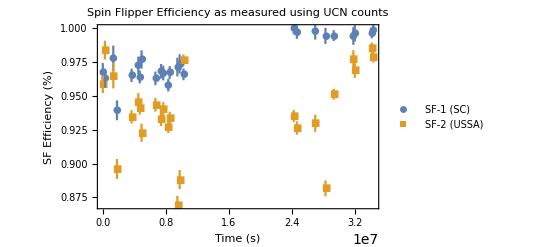

```mathematica
Clear[sfeff1,sfeff2];
sfeff1={};
sfeff2={};
ptdat1=Table[{0,{0,0}},{k,1,runn}];
ptdat2=Table[{0,{0,0}},{k,1,runn}];
For[i=1,i≤runn,i++,
runnum=runNum[[i]];
n12=0;n11=0;n01=0;n02=0;
cydata=ReadList[StringJoin[AscDir,"\\",IntegerString[runnum,10,6],"\\",IntegerString[runnum,10,6],"_Meta3.edm"],metaStructure2];
(**)
ptdat1[[i]][[1]]=AbsoluteTime[cydata[[1]][[1]]];
ptdat2[[i]][[1]]=AbsoluteTime[cydata[[1]][[1]]];
(**)
maxCy=cydata[[-1]][[2]];
(*Print["Run # ",runNum[[i]]," : ",maxCy=cydata[[-1]][[2]]];*)
(**)
For[j=1,j≤(Floor[maxCy/224]*224),j++,
If[cydata[[j]][[25]]==1&&cydata[[j]][[26]]==2,n12+=cydata[[j]][[27]]];
If[cydata[[j]][[25]]==1&&cydata[[j]][[26]]==1,n11+=cydata[[j]][[27]]];
If[cydata[[j]][[25]]==0&&cydata[[j]][[26]]==1,n01+=cydata[[j]][[27]]];
If[cydata[[j]][[25]]==0&&cydata[[j]][[26]]==2,n02+=cydata[[j]][[27]]];
];
ptdat1[[i]][[2]][[1]]=1-Abs[(n12-n11)/(n01+n02)];
ptdat1[[i]][[2]][[2]]=2Abs[((Sqrt[n12]+Sqrt[n11])/(n12+n11))+((Sqrt[n01]+Sqrt[n02])/(n01+n02))];
ptdat2[[i]][[2]][[1]]=1-Abs[(n12-n02)/(n01+n11)];
ptdat2[[i]][[2]][[2]]=2Abs[((Sqrt[n12]+Sqrt[n02])/(n12+n02))+((Sqrt[n01]+Sqrt[n11])/(n01+n11))];
(**)
];
ptdat1[[;;,1]]=N[ptdat1[[;;,1]]-ptdat1[[1]][[1]]];
ptdat2[[;;,1]]=N[ptdat2[[;;,1]]-ptdat2[[1]][[1]]];
EDAListPlot[ptdat1,ptdat2,
Frame->True,FrameLabel->{"Time (s)","SF Efficiency (%)"},PlotMarkers->{Automatic,10},TicksStyle->Directive[FontSize->40],LabelStyle->{Black,18},PlotLegends->{"SF-1 (SC)","SF-2 (USSA)"},PlotLabel->"Spin Flipper Efficiency as measured using UCN counts",ImageSize->{1000},PlotRange->Full]
```

```mathematica
maxCy
Floor[maxCy/224]
Mod[maxCy,224]
Floor[maxCy/224]*224+Mod[maxCy,224]
maxCy-Mod[maxCy,224]
Floor[maxCy/224]*224
```

679.

2

191.

679.

488.

488

```mathematica
AbsoluteTime[cydata[[1]][[1]]]
```

3.672760197995301×10^9

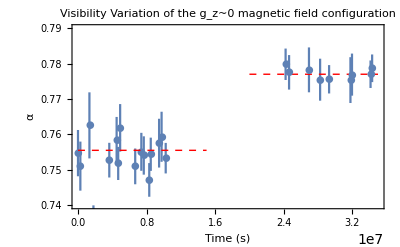

```mathematica
Clear[sfeff1,sfeff2];
sfeff1={};
sfeff2={};
ptdat1=Table[{0,{0,0}},{k,1,runn}];
ptdat2=Table[{0,{0,0}},{k,1,runn}];
For[i=1,i≤runn,i++,
runnum=runNum[[i]];
n12=0;n11=0;n01=0;n02=0;
cydata=ReadList[StringJoin[AscDir,"\\",IntegerString[runnum,10,6],"\\",IntegerString[runnum,10,6],"_Meta3.edm"],metaStructure2];
(**)
ptdat1[[i]][[1]]=AbsoluteTime[cydata[[1]][[1]]];
ptdat2[[i]][[1]]=AbsoluteTime[cydata[[1]][[1]]];
(**)
maxCy=cydata[[-1]][[2]];
(*Print["Run # ",runNum[[i]]," : ",maxCy=cydata[[-1]][[2]]];*)
(**)
For[j=1,j≤(Floor[maxCy/224]*224),j++,
If[cydata[[j]][[25]]==1&&cydata[[j]][[26]]==2,n12+=cydata[[j]][[27]]];
If[cydata[[j]][[25]]==1&&cydata[[j]][[26]]==1,n11+=cydata[[j]][[27]]];
If[cydata[[j]][[25]]==0&&cydata[[j]][[26]]==1,n01+=cydata[[j]][[27]]];
If[cydata[[j]][[25]]==0&&cydata[[j]][[26]]==2,n02+=cydata[[j]][[27]]];
];
ptdat1[[i]][[2]][[1]]=.78(1-Abs[(n12-n11)/(n01+n02)]);
ptdat1[[i]][[2]][[2]]=2Abs[((Sqrt[n12]+Sqrt[n11])/(n12+n11))+((Sqrt[n01]+Sqrt[n02])/(n01+n02))];
(**)
];
ptdat1[[;;,1]]=N[ptdat1[[;;,1]]-ptdat1[[1]][[1]]];
ptdat2[[;;,1]]=N[ptdat2[[;;,1]]-ptdat2[[1]][[1]]];
lineStyle={Thin,Red,Dashed};
line1=Line[{{0,.7555},{1.5×10^7,.7555}}];
line2=Line[{{2×10^7,.777},{3.5×10^7,.777}}];
EDAListPlot[ptdat1,
Frame->True,FrameLabel->{"Time (s)","α"},PlotMarkers->{Automatic,10},TicksStyle->Directive[FontSize->40],LabelStyle->{Black,18},PlotLabel->"Visibility Variation of the g_z~0 magnetic field configuration",ImageSize->{1000},PlotRange->{{0,3.5×10^7},{.74,.79}},Epilog->{Directive[lineStyle],line1,line2}]
```